```mathematica
fgm[x_] := Exp[6 * (Exp[x] - 1)]
```

```mathematica
e1 := fgm'[0]
```

```mathematica
e1
```

6

```mathematica
e1 = fgm'[0]
```

6

```mathematica
ProbDensity=6 x (1-x)
```

```mathematica
e2 = fgm''[0]
```

42

```mathematica
v = e2 - e1 ^2
```

6

```mathematica
v = e2 - (e1) ^2
```

6

```mathematica
Integrate[Exp[t * y] / 20,{y,0,20}]
```

(-1+ⅇ^(20 t))/(20 t)

```mathematica
f'
```

f'

```mathematica
fgm'
```

6 ⅇ^(6 (-1+ⅇ^#1)+#1)&

```mathematica
Plot[(6 ⅇ^(6 (-1+ⅇ^#1)+#1)&)[x],{x,-8,8}]
```

-Graphics-

```mathematica
fgm'[x]
```

```mathematica
fgm''[x]
```

6 ⅇ^(6 (-1+ⅇ^x)+x) (1+6 ⅇ^x)

```mathematica
fgm''[x] // TeXForm
```

6 e^{6 \left(e^x-1\right)+x} \left(6 e^x+1\right)

```mathematica
fgm''[0]
```

42

```mathematica
42 - 36
```

6

```mathematica
f[x_] := Piecewise[{{1 / 20,0 < x && x < 20},{0,x <0 || x ≥ 20}}]
```

```mathematica
Plot[f[x], {x, -2', 2'}]
```

Plot::plln: Limiting value -(0 &) in x-SuperscriptBox[2' is not a machine-sized real number.

Plot[f[x],{x,-2',2'}]

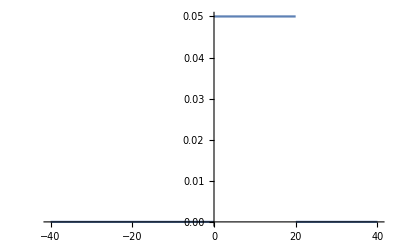

```mathematica
Plot[f[x], {x, -40, 40}]
```

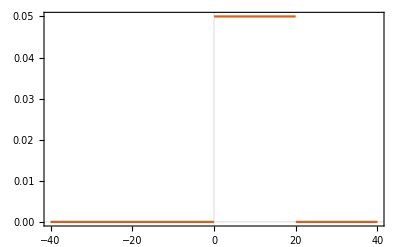

```mathematica
Plot[f[x],{x,-40,40},PlotTheme->"Scientific"]
```

```mathematica
f[x] * x
```

x (Piecewise[{{1/20, 0<x&&x<20}, {0, True}}])

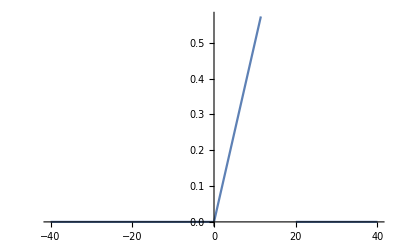

```mathematica
Plot[f[x] * x, {x, -40, 40}]
```

```mathematica
Exp[t * x] * f[x]
```

ⅇ^(t x) (Piecewise[{{1/20, 0<x&&x<20}, {0, True}}])

```mathematica
Plot[Exp[t * x], {t, -40, 40}]
```

-Graphics-

```mathematica
Plot[Exp[t * x], {x, -40, 40}]
```

-Graphics-

```mathematica
Plot[Exp[t * x], {t, -160, 160}]
```

-Graphics-

```mathematica
Plot[Exp[t * 3], {t, -160, 160}]
```

-Graphics-

```mathematica
Plot[Exp[t], {t, -160, 160}]
```

-Graphics-

```mathematica
lot[Exp[t], {t, -40, 40}]
```

lot[ⅇ^t,{t,-40,40}]

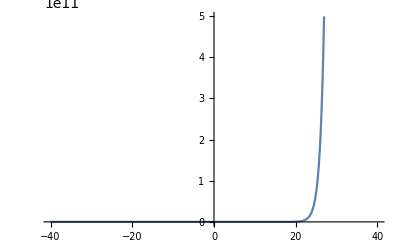

```mathematica
Plot[Exp[t], {t, -40, 40}]
```

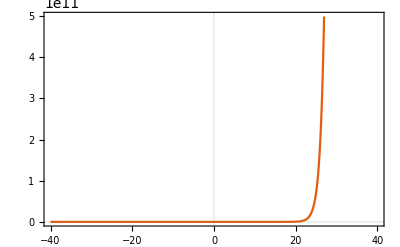

```mathematica
Plot[Exp[t],{t,-40,40},PlotTheme->"Scientific"]
```

```mathematica
Plot[Exp[t * x] * f[x], {t, -100, 100}]
```

-Graphics-

```mathematica
ProbDensity=61 / 20
```

61/20

```mathematica
ProbDensity=1 / 20
```

1/20

```mathematica
ProbDist=ProbabilityDistribution[ProbDensity[x],{x,0,20}];
```

```mathematica
Mean[ProbabilityDistribution[(1/20)[x],{x,0,20}]]
```

Mean[ProbabilityDistribution[1/20[x],{x,0,20}]]

```mathematica
Integrate[Exp[x * t], {x}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {x}.

Integrate[ⅇ^(t x),{x}]

```mathematica
Integrate[Exp[x * t], x]
```

ⅇ^(t x)/t

```mathematica
Integrate[Exp[x * t], x] // TeXForm
```

\frac{e^{t x}}{t}